```mathematica
Cos[A+B]
```

```mathematica
Cos[A+B]//TrigExpand
```

Cos[A] Cos[B]-Sin[A] Sin[B]

```mathematica
Sin[A+B]//TrigExpand
```

Cos[B] Sin[A]+Cos[A] Sin[B]

```mathematica
DSolve[θ'[t]==1/4(1-Cos[θ[t]])-1/2 Sin[θ[t]]+1/2(1+Cos[θ[t]])i,θ[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ[t]→2 ArcTan[1-√(-1+2 i) Tan[1/4 (-√(-1+2 i) t-4 √(-1+2 i) C[1])]]}}

```mathematica
FullSimplify[%2,i>1/2]
```

{{θ[t]→2 ArcTan[1+√(-1+2 i) Tan[1/4 √(-1+2 i) (t+4 C[1])]]}}

```mathematica
%2//Full
```

```mathematica
DSolve[θ'[t]==1/4(1-Cos[θ[t]])+1/2(1+Cos[θ[t]])i,θ[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ[t]→2 ArcTan[√2 √i Tan[1/4 (√2 √i t+4 √2 √i C[1])]]}}

```mathematica
∫_0^π τ/(1/4(1-Cos[θ])-1/2 Sin[θ]+1/2(1+Cos[θ])i)ⅆθ
```

(2 τ (2 ArcTan[1/(√(-1+2 i))]+ⅈ (Log[-(2 ⅈ)/(√(-1+2 i))]-Log[(2 ⅈ)/(√(-1+2 i))])))/(√(-1+2 i))

```mathematica
FullSimplify[%,i>1/2]
```

(2 τ (π+2 ArcCot[√(-1+2 i)]))/(√(-1+2 i))

```mathematica
∫_-π^π τ/(1/4(1-Cos[θ])+1/2(1+Cos[θ])i)ⅆθ
```

4 τ If[(i∉Reals||2 Re[i]>1||0<Re[i]<1/2)&&(i/(2-4 i)∉Reals||Re[i/(2-4 i)]≤-1/4||Re[i/(2-4 i)]≥0),π/(√2 √i),Integrate[1/(1+2 i+(-1+2 i) Cos[θ]),{θ,-π,π},Assumptions→!((i∉Reals||2 Re[i]>1||0<Re[i]<1/2)&&(i/(2-4 i)∉Reals||Re[i/(2-4 i)]≤-1/4||Re[i/(2-4 i)]≥0))]]

```mathematica
FullSimplify[%,i>1/2]
```

(2 √2 π τ)/(√i)

```mathematica
∫_0^π τ/(1/4(1-Cos[θ])-1/2(1+g)Sin[θ]+1/2(1+Cos[θ])i)ⅆθ
```

2 √(-1/(1+2 g+g^2-2 i)) π τ+(4 τ ArcTan[(1+g)/(√(-1-2 g-g^2+2 i))])/(√(-1-2 g-g^2+2 i))

```mathematica
FullSimplify[%,i>1/2]
```

2 √(1/(-(1+g)^2+2 i)) π τ+(4 τ ArcTan[(1+g)/(√(-(1+g)^2+2 i))])/(√(-(1+g)^2+2 i))

```mathematica
∫_0^∞ τ/(-v+1/2 v^2+i)ⅆv
```

2 τ If[√(1-2 i)∉Reals,(π+4 ArcCot[√(-1+2 i)]+2 ⅈ Log[-ⅈ/(√(-1+2 i))]+ⅈ Log[-1+2 i])/(4 √(-1+2 i)),Integrate[1/(2 i+(-2+v) v),{v,0,∞},Assumptions→√(1-2 i)∈Reals]]

```mathematica
FullSimplify[%,i>1/2]
```

(τ (π+2 ArcCot[√(-1+2 i)]))/(√(-1+2 i))

```mathematica
∫_0^∞ τ/(-(1+g)v+1/2 v^2+i)ⅆv
```

2 τ If[(g-√((1+g)^2-2 i)∉Reals||1+Re[g]≤Re[√((1+g)^2-2 i)])&&(g+√((1+g)^2-2 i)∉Reals||Re[g+√((1+g)^2-2 i)]≤-1),(π+4 ArcTan[(1+g)/(√(-(1+g)^2+2 i))]+2 ⅈ Log[-ⅈ/(√(-(1+g)^2+2 i))]+ⅈ Log[-(1+g)^2+2 i])/(4 √(-(1+g)^2+2 i)),Integrate[1/(2 i+v (-2-2 g+v)),{v,0,∞},Assumptions→(Re[g-√(1+2 g+g^2-2 i)]>-1&&g-√(1+2 g+g^2-2 i)∈Reals)||(Re[g+√(1+2 g+g^2-2 i)]>-1&&g+√(1+2 g+g^2-2 i)∈Reals)]]

```mathematica
FullSimplify[%,1+2 g+g^2-2 i>0]
```

2 τ If[1+g≤√((1+g)^2-2 i)&&1+g+√((1+g)^2-2 i)≤0,(π+4 ArcTan[(1+g)/(√(-(1+g)^2+2 i))]+2 ⅈ Log[-ⅈ/(√(-(1+g)^2+2 i))]+ⅈ Log[-(1+g)^2+2 i])/(4 √(-(1+g)^2+2 i)),Integrate[1/(2 i+v (-2-2 g+v)),{v,0,∞},Assumptions→(Re[g-√(1+2 g+g^2-2 i)]>-1&&g-√(1+2 g+g^2-2 i)∈Reals)||(Re[g+√(1+2 g+g^2-2 i)]>-1&&g+√(1+2 g+g^2-2 i)∈Reals)]]

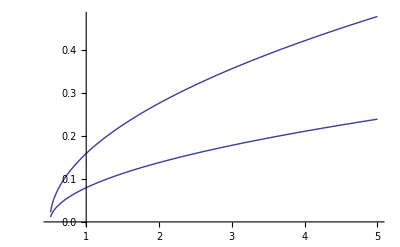

```mathematica
Plot[{1/%14,1/%6}/.τ->1,{i,0.51,5}]
```